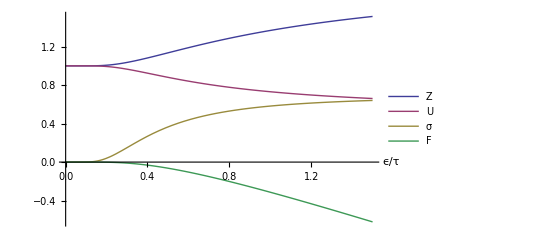

ⅇ^(-ϵ/τ)+1

-τ log(ⅇ^(-ϵ/τ)+1)

ϵ/(ⅇ^(-ϵ/τ)+1)

(ϵ ⅇ^(-ϵ/τ))/(τ (ⅇ^(-ϵ/τ)+1))+log(ⅇ^(-ϵ/τ)+1)

```mathematica
Clear[z, u, f, σ(*, p1, p2, p3*)]
z[t_, e_] = 1 + E^(-e/t) ;
f[t_, e_] = -t Log[z[t, e]] ;
u[t_, e_] = e/z[t, e] ;
σ[t_, e_] = (*Log[z[t, e]]  + (e/t) E^(-e/t)/z[t, e] ;*)
-D[f[t, e], t]  ;

(*p0 = Plot[z[t, 1], {t, 0, 4}, AxesLabel->{ϵ/τ, Z}]  
p1 = Plot[u[t, 1], {t, 0, 4}, AxesLabel->{ϵ/τ, U/ϵ}]  
p2 = Plot[f[t, 1], {t, 0, 4}, AxesLabel->{ϵ/τ, F}] 
p3 = Plot[
σ[t, 1],
{t, 0, 4}, 
AxesLabel->{ϵ/τ, σ}, 
PlotRange -> Full
] *)


Plot[{
z[t, 1], u[t, 1], σ[t, 1], f[t, 1]
}, {t, 0, 1.5}, 
AxesLabel->{ϵ/τ, ""},
PlotRange -> Full,
PlotLegends->
Placed[
{ Z, U, σ, F }
, {0.94, 0.6}] (* Placed so that save graphic shows the legend, even though it looks crappy. *)
]

z[τ, ϵ] // TraditionalForm
f[τ, ϵ] // TraditionalForm
u[τ, ϵ] // TraditionalForm
σ[τ, ϵ] // TraditionalForm
```